```mathematica
m0=5.5;          (*MeV*) 
T0=270;          (*MeV*) 
a0 = 6.75;
a1=-1.95;
a2 =2.625;
a3 =-7.44;
b3 =0.75;
b4=7.5;
 =651 ;       (*MeV*)
G = 10.08*10^-6;       (*MeV^-2*)
Nf=2;
e[p_,z_] :=√(p^2+(m0-G*z)^2);
b2[T_]:=a0 + a1(T0/T)+a2(T0/T)^2+a3(T0/T)^3;
U[x_,T_] := ((-b2[T])/2*x^2-b3/3*(x^3)+b4/4*x^4)*T^4;
 [x_,z_,T_]:=U[x,T]+z^2/2*G-2*Nf*T*NIntegrate[p^2/(2*π^2)*(Log[1+3*x*ⅇ^(-e[p,z]/T)+3*x*ⅇ^(-2*e[p,z]/T)+ⅇ^(-3*e[p,z]/T)]+Log[1+3*x*ⅇ^(-e[p,z]/T)+3*x*ⅇ^(-2*e[p,z]/T)+ⅇ^(-3*e[p,z]/T)]),{p,0,∞}]-6* Nf*NIntegrate[p^2/(2*π^2)*e[p,z] ,{p,0,}];
```

```mathematica
eq[T_]:=FindRoot[{D[Ω[x,z,T],x],D[Ω[x,z,T],z]},{{x,0},{z,-3.17485*10^7}}]
t=350;
{x/.eq[t],z/.eq[t]}//Quiet
```

{0.,-3.17485×10^7}

```mathematica
Tmp=Range[1,600];
pdata={};
n=Length[Tmp];
progress=0;
start=AbsoluteTime[];
PrintTemporary@Dynamic@Row[{ProgressIndicator[progress,{0,n}],"  Running time: ",Round[AbsoluteTime[]-start]," seconds"}];

For[i=1,i<Length[Tmp]+1,i++,AppendTo[pdata,{Tmp[[i]],x/. eq[i],(z/. eq[i])/(-3.17485*10^7)}];
progress=i;];//Quiet

pdata
```

{{1,2.60311×10^-146,1.},{2,3.6054×10^-75,1.},{3,2.43457×10^-51,1.},{4,2.28039×10^-39,1.},{5,3.75912×10^-32,1.},{6,2.56644×10^-27,1.},{7,7.56482×10^-24,1.},{8,3.11397×10^-21,1.},{9,3.43998×10^-19,1.},{10,1.51005×10^-17,1.},{11,3.38273×10^-16,1.},{12,4.5701×10^-15,1.},{13,4.18085×10^-14,1.},{14,2.81362×10^-13,1.},{15,1.48033×10^-12,1.},{16,6.37364×10^-12,1.},{17,2.32573×10^-11,1.},{18,7.3912×10^-11,1.},{19,2.09034×10^-10,1.},{20,5.35263×10^-10,1.},{21,1.25848×10^-9,1.},{22,2.74816×10^-9,1.},{23,5.62696×10^-9,1.},{24,1.08889×10^-8,1.},{25,2.00477×10^-8,1.},{26,3.5316×10^-8,1.},{27,5.98132×10^-8,1.},{28,9.77998×10^-8,1.},{29,1.54933×10^-7,1.},{30,2.38542×10^-7,1.},{31,3.57907×10^-7,1.},{32,5.24556×10^-7,1.},{33,7.52549×10^-7,1.},{34,1.05876×10^-6,1.},{35,1.46317×10^-6,1.},{36,1.9891×10^-6,1.},{37,2.66346×10^-6,1.},{38,3.51697×10^-6,1.},{39,4.58438×10^-6,1.},{40,5.90461×10^-6,1.},{41,7.52092×10^-6,1.},{42,9.48104×10^-6,1.},{43,0.0000118373,1.},{44,0.0000146465,1.},{45,0.0000179703,1.},{46,0.0000218752,1.},{47,0.0000264321,1.},{48,0.0000317169,1.},{49,0.0000378103,1.},{50,0.0000447974,1.},{51,0.0000527681,1.},{52,0.000061817,1.},{53,0.000072043,1.},{54,0.0000835496,1.},{55,0.0000964448,1.},{56,0.000110841,1.},{57,0.000126853,1.},{58,0.000144603,1.},{59,0.000164215,1.},{60,0.000185817,1.},{61,0.000209542,1.},{62,0.000235525,1.},{63,0.000263906,1.},{64,0.000294829,1.},{65,0.000328439,1.},{66,0.000364888,0.999999},{67,0.000404328,0.999999},{68,0.000446917,0.999999},{69,0.000492814,0.999998},{70,0.000542182,0.999998},{71,0.000595188,0.999997},{72,0.000652001,0.999997},{73,0.000712792,0.999996},{74,0.000777738,0.999995},{75,0.000847016,0.999994},{76,0.000920807,0.999993},{77,0.000999295,0.999992},{78,0.00108267,0.999991},{79,0.00117111,0.999989},{80,0.00126482,0.999987},{81,0.00136399,0.999985},{82,0.00146883,0.999983},{83,0.00157952,0.99998},{84,0.00169627,0.999977},{85,0.0018193,0.999973},{86,0.0019488,0.99997},{87,0.002085,0.999965},{88,0.,1.},{89,0.,1.},{90,0.,1.},{91,0.,1.},{92,0.,1.},{93,0.,1.},{94,0.,1.},{95,0.,1.},{96,0.,1.},{97,0.,1.},{98,0.,1.},{99,0.,1.},{100,0.,1.},{101,0.,1.},{102,0.,1.},{103,0.,1.},{104,0.,1.},{105,0.,1.},{106,0.,1.},{107,0.,1.},{108,0.,1.},{109,0.,1.},{110,0.,1.},{111,0.,1.},{112,0.,1.},{113,0.,1.},{114,0.,1.},{115,0.,1.},{116,0.,1.},{117,0.,1.},{118,0.,1.},{119,0.,1.},{120,0.,1.},{121,0.,1.},{122,0.,1.},{123,0.,1.},{124,0.,1.},{125,0.,1.},{126,0.,1.},{127,0.,1.},{128,0.,1.},{129,0.,1.},{130,0.,1.},{131,0.,1.},{132,0.,1.},{133,0.,1.},{134,0.,1.},{135,0.,1.},{136,0.,1.},{137,0.,1.},{138,0.,1.},{139,0.,1.},{140,0.,1.},{141,0.,1.},{142,0.,1.},{143,0.,1.},{144,0.,1.},{145,0.,1.},{146,0.,1.},{147,0.,1.},{148,0.,1.},{149,0.,1.},{150,0.,1.},{151,0.,1.},{152,0.,1.},{153,0.,1.},{154,0.,1.},{155,0.,1.},{156,0.,1.},{157,0.,1.},{158,0.,1.},{159,0.,1.},{160,0.,1.},{161,0.,1.},{162,0.,1.},{163,0.,1.},{164,0.,1.},{165,0.,1.},{166,0.,1.},{167,0.,1.},{168,0.,1.},{169,0.,1.},{170,0.,1.},{171,0.,1.},{172,0.,1.},{173,0.,1.},{174,0.,1.},{175,0.,1.},{176,0.,1.},{177,0.,1.},{178,0.,1.},{179,0.,1.},{180,0.,1.},{181,0.,1.},{182,0.,1.},{183,0.,1.},{184,0.,1.},{185,0.,1.},{186,0.,1.},{187,0.,1.},{188,0.,1.},{189,0.,1.},{190,0.,1.},{191,0.,1.},{192,0.,1.},{193,0.,1.},{194,0.,1.},{195,0.,1.},{196,0.,1.},{197,0.,1.},{198,0.,1.},{199,0.,1.},{200,0.,1.},{201,0.,1.},{202,0.,1.},{203,0.,1.},{204,0.,1.},{205,0.,1.},{206,0.,1.},{207,0.,1.},{208,0.,1.},{209,0.,1.},{210,0.,1.},{211,0.,1.},{212,0.,1.},{213,0.,1.},{214,0.,1.},{215,0.,1.},{216,0.,1.},{217,0.,1.},{218,0.,1.},{219,0.,1.},{220,0.,1.},{221,0.,1.},{222,0.,1.},{223,0.,1.},{224,0.,1.},{225,0.,1.},{226,0.,1.},{227,0.,1.},{228,0.,1.},{229,0.,1.},{230,0.,1.},{231,0.,1.},{232,0.,1.},{233,0.,1.},{234,0.,1.},{235,0.,1.},{236,0.,1.},{237,0.,1.},{238,0.,1.},{239,0.,1.},{240,0.,1.},{241,0.,1.},{242,0.,1.},{243,0.,1.},{244,0.,1.},{245,0.,1.},{246,0.,1.},{247,0.,1.},{248,0.,1.},{249,0.,1.},{250,0.,1.},{251,0.,1.},{252,0.,1.},{253,0.,1.},{254,0.,1.},{255,0.,1.},{256,0.,1.},{257,0.,1.},{258,0.,1.},{259,0.,1.},{260,0.,1.},{261,0.,1.},{262,0.,1.},{263,-0.168912,1.23998},{264,-0.146666,1.21079},{265,-0.259739,1.37761},{266,-0.233479,1.34334},{267,-0.212388,1.3159},{268,-0.195077,1.29345},{269,-0.180615,1.27477},{270,-0.168352,1.259},{271,-0.157823,1.24553},{272,-0.215092,1.31091},{273,-0.232282,1.33251},{274,-0.204845,1.30132},{275,-0.245401,1.35337},{276,-0.223467,1.32873},{277,-0.296766,1.42602},{278,-0.274496,1.40151},{279,-0.256459,1.38173},{280,-0.241457,1.36537},{281,-0.228721,1.35156},{282,-0.21773,1.33971},{283,-0.251965,1.38127},{284,-0.264489,1.39872},{285,-0.316572,1.46567},{286,-0.278752,1.42476},{287,-0.267164,1.41719},{288,-0.271001,1.42924},{289,-0.259134,1.42457},{290,-0.278251,1.45662},{291,-0.299511,1.49175},{292,-0.323425,1.53044},{293,-0.350847,1.5735},{294,-0.300303,1.52662},{295,-0.327389,1.57165},{296,-0.303074,1.55993},{297,-0.295697,1.56867},{298,-0.297809,1.58858},{299,-0.284621,1.5927},{300,-0.296631,1.62376},{301,-0.308035,1.65405},{302,-0.630301,2.3513},{303,-0.621015,2.34425},{304,-0.612127,2.33775},{305,-0.603614,2.33177},{306,-0.595451,2.32629},{307,-0.587619,2.32126},{308,-0.580097,2.31667},{309,-0.572867,2.31249},{310,-0.565914,2.30871},{311,-0.559222,2.30529},{312,-0.552775,2.30223},{313,-0.546563,2.2995},{314,-0.540571,2.29709},{315,-0.534789,2.29498},{316,-0.529205,2.29316},{317,-0.52381,2.29161},{318,-0.518595,2.29033},{319,-0.513551,2.2893},{320,-0.50867,2.2885},{321,-0.503944,2.28794},{322,-0.499365,2.2876},{323,-0.494928,2.28747},{324,-0.490625,2.28755},{325,0.,1.},{326,0.,1.},{327,0.,1.},{328,0.,1.},{329,0.,1.},{330,0.,1.},{331,0.,1.},{332,0.,1.},{333,0.,1.},{334,0.,1.},{335,0.,1.},{336,0.,1.},{337,0.,1.},{338,0.,1.},{339,0.,1.},{340,0.,1.},{341,0.,1.},{342,0.,1.},{343,0.,1.},{344,0.,1.},{345,0.,1.},{346,0.,1.},{347,0.,1.},{348,0.,1.},{349,0.,1.},{350,0.,1.},{351,0.,1.},{352,0.,1.},{353,0.,1.},{354,0.,1.},{355,0.,1.},{356,0.,1.},{357,0.,1.},{358,0.,1.},{359,0.,1.},{360,0.,1.},{361,0.,1.},{362,0.,1.},{363,0.,1.},{364,0.,1.},{365,0.,1.},{366,0.,1.},{367,0.,1.},{368,0.,1.},{369,0.,1.},{370,0.,1.},{371,0.,1.},{372,0.,1.},{373,0.,1.},{374,0.,1.},{375,0.,1.},{376,0.,1.},{377,0.,1.},{378,0.,1.},{379,0.,1.},{380,0.,1.},{381,0.,1.},{382,0.,1.},{383,0.,1.},{384,0.,1.},{385,0.,1.},{386,0.,1.},{387,0.,1.},{388,0.,1.},{389,0.,1.},{390,0.,1.},{391,0.,1.},{392,0.,1.},{393,0.,1.},{394,0.,1.},{395,0.,1.},{396,0.,1.},{397,0.,1.},{398,0.,1.},{399,0.,1.},{400,0.,1.},{401,0.,1.},{402,0.,1.},{403,0.,1.},{404,0.,1.},{405,0.,1.},{406,0.,1.},{407,0.,1.},{408,0.,1.},{409,0.,1.},{410,0.,1.},{411,0.,1.},{412,0.,1.},{413,0.,1.},{414,0.,1.},{415,0.,1.},{416,0.,1.},{417,0.,1.},{418,0.,1.},{419,0.,1.},{420,0.,1.},{421,0.,1.},{422,0.,1.},{423,0.,1.},{424,0.,1.},{425,0.,1.},{426,0.,1.},{427,0.,1.},{428,0.,1.},{429,0.,1.},{430,0.,1.},{431,0.,1.},{432,0.,1.},{433,0.,1.},{434,0.,1.},{435,0.,1.},{436,0.,1.},{437,0.,1.},{438,0.,1.},{439,0.,1.},{440,0.,1.},{441,0.,1.},{442,0.,1.},{443,0.,1.},{444,0.,1.},{445,0.,1.},{446,0.,1.},{447,0.,1.},{448,0.,1.},{449,0.,1.},{450,0.,1.},{451,0.,1.},{452,0.,1.},{453,0.,1.},{454,0.,1.},{455,0.,1.},{456,0.,1.},{457,0.,1.},{458,0.,1.},{459,0.,1.},{460,0.,1.},{461,0.,1.},{462,0.,1.},{463,0.,1.},{464,0.,1.},{465,0.,1.},{466,0.,1.},{467,0.,1.},{468,0.,1.},{469,0.,1.},{470,0.,1.},{471,0.,1.},{472,0.,1.},{473,0.,1.},{474,0.,1.},{475,0.,1.},{476,0.,1.},{477,0.,1.},{478,0.,1.},{479,0.,1.},{480,0.,1.},{481,0.,1.},{482,0.,1.},{483,0.,1.},{484,0.,1.},{485,0.,1.},{486,0.,1.},{487,0.,1.},{488,0.,1.},{489,0.,1.},{490,0.,1.},{491,0.,1.},{492,0.,1.},{493,0.,1.},{494,0.,1.},{495,0.,1.},{496,0.,1.},{497,0.,1.},{498,0.,1.},{499,0.,1.},{500,0.,1.},{501,0.,1.},{502,0.,1.},{503,0.,1.},{504,0.,1.},{505,0.,1.},{506,0.,1.},{507,0.,1.},{508,0.,1.},{509,0.,1.},{510,0.,1.},{511,0.,1.},{512,0.,1.},{513,0.,1.},{514,0.,1.},{515,0.,1.},{516,0.,1.},{517,0.,1.},{518,0.,1.},{519,0.,1.},{520,0.,1.},{521,0.,1.},{522,0.,1.},{523,0.,1.},{524,0.,1.},{525,0.,1.},{526,0.,1.},{527,0.,1.},{528,0.,1.},{529,0.,1.},{530,0.,1.},{531,0.,1.},{532,0.,1.},{533,0.,1.},{534,0.,1.},{535,0.,1.},{536,0.,1.},{537,0.,1.},{538,0.,1.},{539,0.,1.},{540,0.,1.},{541,0.,1.},{542,0.,1.},{543,0.,1.},{544,0.,1.},{545,0.,1.},{546,0.,1.},{547,0.,1.},{548,0.,1.},{549,0.,1.},{550,0.,1.},{551,0.,1.},{552,0.,1.},{553,0.,1.},{554,0.,1.},{555,0.,1.},{556,0.,1.},{557,0.,1.},{558,0.,1.},{559,0.,1.},{560,0.,1.},{561,0.,1.},{562,0.,1.},{563,0.,1.},{564,0.,1.},{565,0.,1.},{566,0.,1.},{567,0.,1.},{568,0.,1.},{569,0.,1.},{570,0.,1.},{571,0.,1.},{572,0.,1.},{573,0.,1.},{574,0.,1.},{575,0.,1.},{576,0.,1.},{577,0.,1.},{578,0.,1.},{579,0.,1.},{580,0.,1.},{581,0.,1.},{582,0.,1.},{583,0.,1.},{584,0.,1.},{585,0.,1.},{586,0.,1.},{587,0.,1.},{588,0.,1.},{589,0.,1.},{590,0.,1.},{591,0.,1.},{592,0.,1.},{593,0.,1.},{594,0.,1.},{595,0.,1.},{596,0.,1.},{597,0.,1.},{598,0.,1.},{599,0.,1.},{600,0.,1.}}

```mathematica
Import["C:\\Users\\mubas\\OneDrive\\Desktop\\PNJL_Thesis\\polyakovloop_data.csv","List"]
```

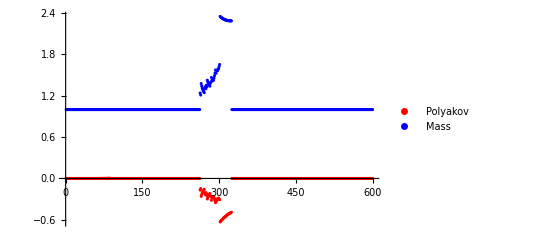

```mathematica
(*all parameters form the above data*)
Tmp = pdata[[All,1]];
polyakov=pdata[[All,2]];
mass = pdata[[All,3]];
ListPlot[{Transpose[{Tmp,polyakov}],Transpose[{Tmp,mass}]},PlotStyle->{Red,Blue},PlotLegends->{"Polyakov","Mass"},PlotRange->All]
```